```mathematica
Quit[]
```

# Calculations

```mathematica
<<FeynCalc`
```

FeynCalc 9.2.0. For help, use the documentation center, check out the wiki or write to the mailing list.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, Comput. Phys. Commun., 207C, 432-444, 2016, arXiv:1601.01167

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun., 64, 345-359, 1991.

Calculations

## Initial constants

```mathematica
Y=1/2;
Gf=1.166*10^(-5);
dm232=1;
a1=1.07;
Fm2320=1/(3*π);
mπ=0.13957061;
fπ=0.1304;
mρ=0.7665;
fρ=0.216;
ma1=1.230;
fa1=0.238;
SetAttributes[V,Orderless];
V["c","b"]=0.0411;V["c","s"]=0.974;V["c","d"]=0.225;
V["u","b"]=0.00357;V["u","s"]=0.225;V["u","d"]=0.974;
```

## Clear

```mathematica
Clear[Fq3π1,Fq2π,Fq3π,Fq4π,Fq5π,Γ2π,Γ3π,Γ4π,Γ5π,dΓ2π,dΓ3π,dΓ3π1,dΓ4π,dΓ5π,H,cH,H2,H3,H4,H6,HT,λ,p1,p2,q2,q,m1,m2];
ClearScalarProducts;
```

## Init

```mathematica
Clear[H,cH,H2,H3,H4,H6,HT,λ,p1,p2,m232,q,m1,m2,m3,m4, Fq3π,Fq5π,Br,f1,f2,g1,g2];
ScalarProduct[p11,p11]=m1^2;
ScalarProduct[p22,p22]=m2^2;
ScalarProduct[p11,p22]=(m1^2+m2^2-m232)/2;
SetMandelstam[m232,m132,m122,p1,-p2,-pe,-ke,m1,m2,0,0];
qq=p11-p22;
q=p1-p2;
sigma=I*(GA[μ].GA[ν]-GA[ν].GA[μ])/2;
H =SpinorUBar[p22,m2].(GA[μ]*f1+I*sigma*FV[qq,ν]*f2/m1).SpinorU[p11, m1]-SpinorUBar[p22,m2].(GA[μ]*g1+ⅈ*sigma*FV[qq,ν]*g2/m1).GA[5].SpinorU[p11, m1];
HH=SpinorUBar[p2,m2].(GA[μ]*f1+I*sigma*FV[q,ν]*f2/m1).SpinorU[p1, m1]-SpinorUBar[p2,m2].(GA[μ]*g1+ⅈ*sigma*FV[q,ν]*g2/m1).GA[5].SpinorU[p1, m1];
cH= ComplexConjugate[H]/.{μ->α,ν->β};
cHH= ComplexConjugate[HH]/.{μ->α,ν->β};
H2=H*cH;
HH2=HH*cHH;
HH3=DiracSimplify[FermionSpinSum[HH2]]/.{DiracTrace->TR};
H3=DiracSimplify[FermionSpinSum[H2]]/.{DiracTrace->TR};
H6=Simplify[Calc[H3]];
H4=Simplify[Calc[H3*(FV[qq,μ]*FV[qq,α]-m232*MT[μ,α])]];
λ:=√(1-((m2+√m232)/m1)^2)*√(1-((m2-√m232)/m1)^2);
HT:=λ*H4;
(*T=Transversal*)
HL:=λ*Simplify[Calc[H3*(FV[qq,μ]*FV[qq,α])]];
(*L=Longitudinal*)
L=SpinorUBar[pe].GA[μ].(1+GA[5]).SpinorV[ke];
cL=ComplexConjugate[L]/.{μ->α};
L2=FermionSpinSum[L*cL]/.{DiracTrace->TR};
M2=Simplify[1/2*Gf^2*Calc[HH3*L2]];
M3=M2//.m132->m1^2+m2^2-m122-m232;
E2ZV= (m122-m2^2 +m3^2)/(2*Sqrt[m122]) (*  E2^*  *);
E3ZV= (m1^2-m122-m4^2)/(2*Sqrt[m122])  (*  E3^*  *);
m23min=(E2ZV+E3ZV)^2-(Sqrt[E2ZV^2-m3^2]+Sqrt[E3ZV^2-m4^2])^2;
m23max=Simplify[Calc[(E2ZV+E3ZV)^2-(Sqrt[E2ZV^2-m3^2]-Sqrt[E3ZV^2-m4^2])^2]];
m12min=m2^2;
m12max=m1^2;
dΓl:= (Gf^2/2)*(1/(2*Y+1))*(1/(2*m1))*dm232 /(2*π)*(1/(8*π))*Vckm^2*HT*Fm2320
dΓl1:=(1/2)*(1/(2*π)^3)*(1/(32*m1^3))*Vckm^2*M3;
```

## File

```mathematica
SetDirectory[NotebookDirectory[]];
<<"wang_data.m";
decays={#["in"],#["out"]}&/@Normal[DeleteDuplicates[dsFF[All,{"in","out"}]]];
Clear[$FF];
$FF[data_]:=Module[{},Switch[data["func"],"FF",Return[data["F0"]/(1-m232/data["mFit"]^2+data["delta"] (m232/data["mFit"]^2)^2)];,"GG",Return[data["F0"]/(1+m232/data["mFit"]^2+data["delta"] (m232/data["mFit"]^2)^2)];];];
(*Clear[cS,cA];*)
Clear[FF];
FF[query_]:=Module[{$res},$res=dsFF[query];
Return[cS $FF[$res[1]]+cA $FF[$res[2]]]];
```

## Test

```mathematica
in="\\Omega_{cc}^{+}";
out="\\Omega_{c}^{0}";
Clear[m1,m2,quark1,quark2,f1,f2,g1,g2,Vckm,cS,cA];
m1=dsParticles[in]["mass"]; m2=dsParticles[out]["mass"];
cA=cA1[out,in];cS=cS1[out,in];
f1=FF[Select[#in==in&&#out==out&&#f=="f1"&]];
f2=FF[Select[#in==in&&#out==out&&#f=="f2"&]];
g1=FF[Select[#in==in&&#out==out&&#f=="g1"&]];
g2=FF[Select[#in==in&&#out==out&&#f=="g2"&]];
quark1=Characters[Quarks[in]];
quark2=Characters[Quarks[out]];
Vckm1=First[(quark1[[1]]-quark2[[1]])+(quark1[[2]]-quark2[[2]])+(quark1[[3]]-quark2[[3]])];
quarkrazn=(quark1[[1]]-quark2[[1]])+(quark1[[2]]-quark2[[2]])+(quark1[[3]]-quark2[[3]]);
Vckm2=-quarkrazn+Vckm1;
Vckm=V[Vckm1,Vckm2];
m3=0; m4=0;
Γl1=NIntegrate[dΓl, {m232,0,(m1-m2)^2}];
Γl2=NIntegrate[dΓl1,{m122,m12min,m12max},{m232,m23min,m23max}];
```

```mathematica
m1= 3.78663;
m2= 2.6952;
```

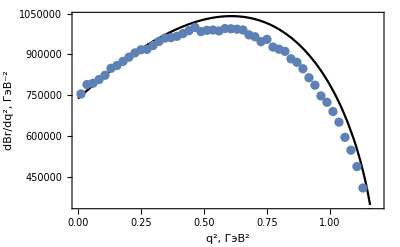

```mathematica
SetDirectory[NotebookDirectory[]];
tab=ReadList["m2_23.txt",{Number,Number,Number}];
tab=tab[[All,1;;2]];
{x,y}={tab[[10,1]],tab[[10,2]]};
y0=dΓl/.m232-> x;
pic1 = Plot[dΓl*y/y0,{m232,0,(m1-m2)^2},PlotStyle->Black,FrameLabel->{"q^2, (:0413:044d:0412)^2","dBr/dq^2, (:0413:044d:0412)^-2"}, Frame-> True ];
pic2=ListPlot[tab];
Show[pic1, pic2]
```

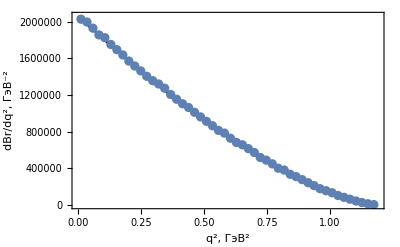

```mathematica
Clear[f1,f2,g1,g2];
f1=1; f2=0; g1=0;g2=0;
SetDirectory["/home/anton/Dropbox/evtgen/baryons"];
Clear[tab,pic1,pic2];
tab=ReadList["m2_23f1.txt",{Number,Number,Number}];
tab=tab[[All,1;;2]];
{x,y}={tab[[10,1]],tab[[10,2]]};
y0=dΓl/.m232-> x;
pic1 = Plot[dΓl*y/y0,{m232,0,(m1-m2)^2},PlotStyle->Black,FrameLabel->{"q^2, (:0413:044d:0412)^2","dBr/dq^2, (:0413:044d:0412)^-2"}, Frame-> True ];
pic2=ListPlot[tab];
Show[pic1, pic2]
```

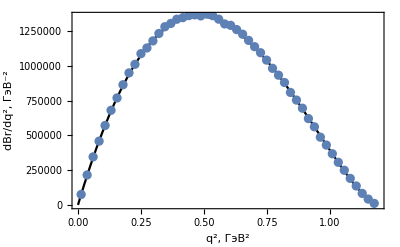

```mathematica
Clear[f1,f2,g1,g2];
f1=0; f2=1; g1=0;g2=0;
SetDirectory["/home/anton/Dropbox/evtgen/baryons"];
Clear[tab];
tab2=ReadList["m2_23f2.txt",{Number,Number,Number}];
tab2=tab2[[All,1;;2]];
{x,y}={tab2[[10,1]],tab2[[10,2]]};
y0=dΓl/.m232-> x;
pic1 = Plot[dΓl*y/y0,{m232,0,(m1-m2)^2},PlotStyle->Black,FrameLabel->{"q^2, (:0413:044d:0412)^2","dBr/dq^2, (:0413:044d:0412)^-2"}, Frame-> True ];
pic2=ListPlot[tab2];
Show[pic1, pic2]
```

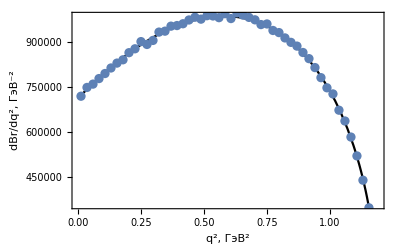

```mathematica
Clear[f1,f2,g1,g2];
f1=0; f2=0; g1=1;g2=0;
SetDirectory["/home/anton/Dropbox/evtgen/baryons"];
Clear[tab];
tab2=ReadList["m2_23g1.txt",{Number,Number,Number}];
tab2=tab2[[All,1;;2]];
{x,y}={tab2[[10,1]],tab2[[10,2]]};
y0=dΓl/.m232-> x;
pic1 = Plot[dΓl*y/y0,{m232,0,(m1-m2)^2},PlotStyle->Black,FrameLabel->{"q^2, (:0413:044d:0412)^2","dBr/dq^2, (:0413:044d:0412)^-2"}, Frame-> True ];
pic2=ListPlot[tab2];
Show[pic1, pic2]
```

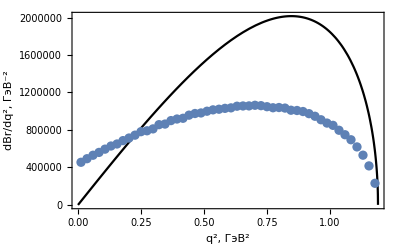

```mathematica
Clear[f1,f2,g1,g2];
f1=0; f2=0; g1=0;g2=1;
SetDirectory["/home/anton/Dropbox/evtgen/baryons"];
Clear[tab];
tab2=ReadList["m2_23g2.txt",{Number,Number,Number}];
tab2=tab2[[All,1;;2]];
{x,y}={tab2[[10,1]],tab2[[10,2]]};
y0=dΓl/.m232-> x;
pic1 = Plot[dΓl*y/y0,{m232,0,(m1-m2)^2},PlotStyle->Black,FrameLabel->{"q^2, (:0413:044d:0412)^2","dBr/dq^2, (:0413:044d:0412)^-2"}, Frame-> True ];
pic2=ListPlot[tab2];
Show[pic1, pic2]
```

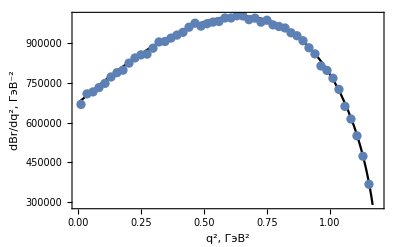

```mathematica
Clear[f1,f2,g1,g2];
f1=FF[Select[#in==in&&#out==out&&#f=="f1"&]];
f2=FF[Select[#in==in&&#out==out&&#f=="f2"&]];
g1=FF[Select[#in==in&&#out==out&&#f=="g1"&]];
g2=0;
SetDirectory["/home/anton/Dropbox/evtgen/baryons"];
Clear[tab];
tab2=ReadList["m2_23testg2=0.txt",{Number,Number,Number}];
tab2=tab2[[All,1;;2]];
{x,y}={tab2[[10,1]],tab2[[10,2]]};
y0=dΓl/.m232-> x;
pic1 = Plot[dΓl*y/y0,{m232,0,(m1-m2)^2},PlotStyle->Black,FrameLabel->{"q^2, (:0413:044d:0412)^2","dBr/dq^2, (:0413:044d:0412)^-2"}, Frame-> True ];
pic2=ListPlot[tab2];
Show[pic1, pic2]
```

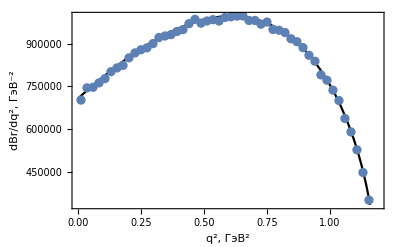

```mathematica
Clear[f1,f2,g1,g2];
f1=FF[Select[#in==in&&#out==out&&#f=="f1"&]];
f2=FF[Select[#in==in&&#out==out&&#f=="f2"&]];
g1=FF[Select[#in==in&&#out==out&&#f=="g1"&]];
g2=FF[Select[#in==in&&#out==out&&#f=="g2"&]];
SetDirectory["/home/anton/Dropbox/evtgen/baryons"];
Clear[tab];
tab2=ReadList["m2_23.txt",{Number,Number,Number}];
tab2=tab2[[All,1;;2]];
{x,y}={tab2[[10,1]],tab2[[10,2]]};
y0=dΓl/.m232-> x;
pic1 = Plot[dΓl*y/y0,{m232,0,(m1-m2)^2},PlotStyle->Black,FrameLabel->{"q^2, (:0413:044d:0412)^2","dBr/dq^2, (:0413:044d:0412)^-2"}, Frame-> True ];
pic2=ListPlot[tab2];
Show[pic1, pic2]
```